/home/tyler/Documents/UW/AU17/stoch/hw1/img/interval.pdf

/home/tyler/Documents/UW/AU17/stoch/hw1/img/inverse.pdf

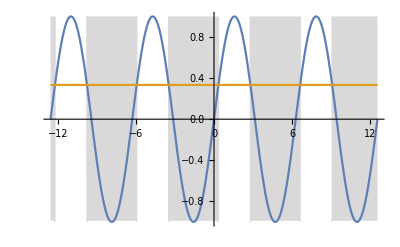

```mathematica
Export[NotebookDirectory[]<>"img/interval.pdf",
Show[{
Plot[If[Sin[x]≤1/3,-1,1],{x,-4Pi,4Pi},PlotStyle->White,Filling->Top,FillingStyle->LightGray],Plot[{Sin[x],1/3},{x,-4Pi,4Pi},Filling->{3->1}]
}]
]
Export[NotebookDirectory[]<>"img/inverse.pdf",
Show[{
Plot[{Sin[x],1/3},{x,-4Pi,4Pi}],
Plot[Sin[x],{x,-Pi/2,Pi/2},PlotStyle->Red],
Plot[-1/3,{x,-4Pi,4Pi},PlotStyle->{Gray,Dashed}]
}]
]
```